```mathematica
G[n_]:=((2n+1)/(2n-√n))^(√(n + 2))
```

```mathematica
Limit[G[n], n -> ∞]
```

√ⅇ

EJERCICIO 2:

```mathematica
Limit[(√(n^5)-√(n^3+1))/Log[n], n-> ∞]
```

∞

concluimos que An >> Bn;

EJERCICIO 3:

```mathematica
a[n_]:=If[n==1,2,1+1/(3a[n - 1])]
```

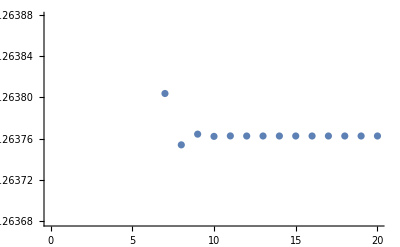

```mathematica
ListPlot[Table[a[n],{n,1,20}]]
```

EJERCICIO 4:

```mathematica
b[n_]:=If[n==1,3,√(5+4b[n-1])]
```

```mathematica
b[15]
```

√(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √(5+4 √17)))))))))))))

```mathematica
N[b[15],20]
```

4.999993739408938254

EJERCICIO 5:

```mathematica
c[n_]:=If[n==1,1,2a[n-1]+1]
```

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[n+1]==2a[n]+1,a[1]==1},a[n],n]
```

{{a[n]→-1+2^n}}

EJERCICIO 6:

```mathematica
RSolve[(2a[n + 2]==3a[n]+a[n+1],a[1]==1, a[2]==1),a[n],n]
```

```mathematica
Clear[a]
```

```mathematica
RSolve[{2a[n + 2]==3a[n]+a[n+1],a[1]==1, a[2]==1},a[n],n]
```

{{a[n]→-1/15 2^-n (3 (-2)^n-8 3^n)}}

```mathematica
Limit[(-1/5*(-1^n)+8/15*(3/2)^n)/(3/2)^n,n->Infinity]
```

8/15

```mathematica
N[%]
```

0.533333